```mathematica
ϵ[n_, kz_]:=w kz + Sign[n] Sqrt[α^2 v^2 kz^2 + Abs[n] α^3 ω^2]
```

```mathematica
ϵ[n, kz]/.{v->1, w->β, α->Sqrt[1-β^2]}
```

kz β+√(kz^2 (1-β^2)+(1-β^2)^(3/2) ω^2 Abs[n]) Sign[n]

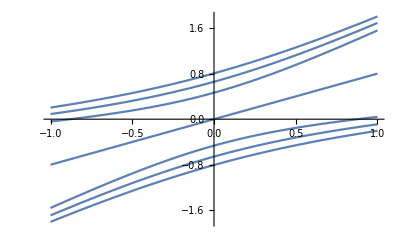

```mathematica
Plot[
Table[
ϵ[n, kz]/.{v->1, w->β, α->Sqrt[1-β^2]}/.{β->0.8, n->n, ω->1},
{n,-3, 3}
],
{kz, -1,1}
]
```

```mathematica
Manipulate[
Plot[
Table[
ϵ[n, kz]/.{v->1, w->β, α->Sqrt[1-β^2]}/.{β->0.8, n->n, ω->1},
{n,-3, 3}
],
{kz, -1,1}
], 
{β, 0, 1.3}
]
```

```mathematica
v={vx,vy,vz};
k={kx,ky,kz};
Hii=w kx IdentityMatrix[2] + Sum[v[[i]] k[[i]] PauliMatrix[i], {i, 3}];
```

```mathematica
Hii//MatrixForm
```

(kz vz+kx w | kx vx-ⅈ ky vy
kx vx+ⅈ ky vy | -kz vz+kx w)

```mathematica
Eigenvalues[Hii]
```

{-√(kx^2 vx^2+ky^2 vy^2+kz^2 vz^2)+kx w,√(kx^2 vx^2+ky^2 vy^2+kz^2 vz^2)+kx w}

```mathematica
Eigenvalues[
KroneckerProduct[PauliMatrix[1], Hii]
]
```

{-√(kx^2 vx^2+ky^2 vy^2+kz^2 vz^2)-kx w,√(kx^2 vx^2+ky^2 vy^2+kz^2 vz^2)-kx w,-√(kx^2 vx^2+ky^2 vy^2+kz^2 vz^2)+kx w,√(kx^2 vx^2+ky^2 vy^2+kz^2 vz^2)+kx w}

```mathematica
Eigenvalues[
KroneckerProduct[PauliMatrix[3], Hii]
]
```

{-√(kx^2 vx^2+ky^2 vy^2+kz^2 vz^2)-kx w,√(kx^2 vx^2+ky^2 vy^2+kz^2 vz^2)-kx w,-√(kx^2 vx^2+ky^2 vy^2+kz^2 vz^2)+kx w,√(kx^2 vx^2+ky^2 vy^2+kz^2 vz^2)+kx w}